This notebook generates spliced-read performance plots for a given sample. REQUIRES UNIX-BASED OS. Enter the directory where “.perform” files may be found below.

```mathematica
SetDirectory["/Users/anellore/paper_perform"];
```

```mathematica
(*Select sample*)
```

```mathematica
sampleName="NA18508.1.M_111124_1"
```

NA18508.1.M_111124_1

```mathematica
(*Read pro file for coverage*)
```

```mathematica
TPMs=Import[sampleName~~"_sim.pro"][[All, {6,10}]];
```

```mathematica
(*Compute TPMs*)
```

```mathematica
For[i=1, i≤2, i+=1,TPMs[[All, i]] =N[sampleCoverage[[All, i]] / Total[sampleCoverage[[All, i]]]]*10^6];
```

```mathematica
sortedOriginalTPMs=Reverse[Sort[Transpose[TPMs][[1]]]];
```

```mathematica
sortedSimTPMs = Reverse[Sort[Transpose[TPMs][[2]]]];
```

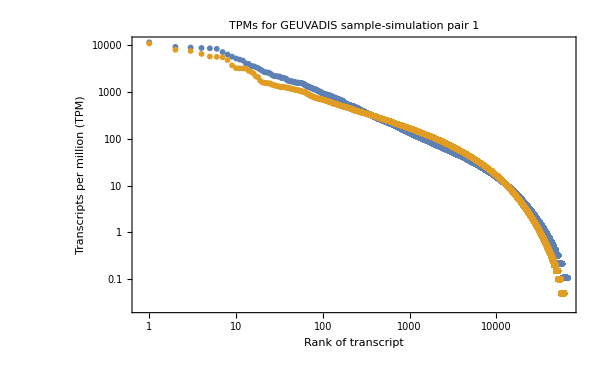

```mathematica
ListLogLogPlot[{sortedOriginalTPMs, sortedSimTPMs}, PlotRange->All, Frame->True, PlotLegends->LineLegend["Expressions"], FrameLabel->{"Rank of transcript","Transcripts per million (TPM)"},
PlotLabel->Style["TPMs for GEUVADIS sample-simulation pair 1", 15, FontFamily->"Futura"],ImageSize->{600,500},FrameStyle->{Directive[FontFamily->"Bodoni", FontSize->18,Black], Directive[FontFamily->"Bodoni", FontSize->18]}, PlotStyle->PointSize[.007]]
```

```mathematica
Correlation[sampleCoverage[[All,1]], sampleCoverage[[All,2]]]
```

0.885803

```mathematica
sampleCoverage[[All, {6,9}]]
```

{{4,3.49995×10^-7},{0,0.},{0,0.},{0,0.},{1,0.},{3,0.},{0,0.},{0,0.},{0,0.},{1,1.99997×10^-7},{0,0.},{0,0.},{0,0.},183023,{0,0.},{0,0.},{0,0.},{1,1.49998×10^-7},{0,0.},{5,5.49993×10^-7},{0,0.},{6,2.49997×10^-7},{0,0.},{0,0.},{4,1.49998×10^-7},{4,3.49995×10^-7},{0,0.}}
 |  |  |  |

```mathematica
performanceFiles = DeleteCases[Select[FileNames["*"],(StringFreeQ[#,"summary"]&)], StringFreeQ[#,sampleName]&]
```

{NA18508.1.M_111124_1.rail.perform,NA18508.1.M_111124_1.star.ann_paired_1pass.perform,NA18508.1.M_111124_1.star.ann_paired_2pass.perform,NA18508.1.M_111124_1.star.ann_single_1pass.perform,NA18508.1.M_111124_1.star.ann_single_2pass.perform,NA18508.1.M_111124_1.star.noann_paired_1pass.perform,NA18508.1.M_111124_1.star.noann_paired_2pass.perform,NA18508.1.M_111124_1.star.noann_single_1pass.perform,NA18508.1.M_111124_1.star.noann_single_2pass.perform,NA18508.1.M_111124_1.tophat.ann_paired.perform,NA18508.1.M_111124_1.tophat.ann_single.perform,NA18508.1.M_111124_1.tophat.noann_paired.perform,NA18508.1.M_111124_1.tophat.noann_single.perform,NA18861.1.M_120209_2.rail.perform,NA18861.1.M_120209_2.star.ann_paired_1pass.perform,NA18861.1.M_120209_2.star.ann_paired_2pass.perform,NA18861.1.M_120209_2.star.ann_single_1pass.perform,NA18861.1.M_120209_2.star.ann_single_2pass.perform,NA18861.1.M_120209_2.star.noann_paired_1pass.perform,NA18861.1.M_120209_2.star.noann_paired_2pass.perform,NA18861.1.M_120209_2.star.noann_single_1pass.perform,NA18861.1.M_120209_2.star.noann_single_2pass.perform,NA18861.1.M_120209_2.tophat.ann_paired.perform,NA18861.1.M_120209_2.tophat.ann_single.perform,NA18861.1.M_120209_2.tophat.noann_paired.perform,NA18861.1.M_120209_2.tophat.noann_single.perform}

```mathematica
verboseNameRules = {sampleName~~".rail.perform"->"Rail-RNA", sampleName~~".star.ann_paired_1pass.perform"->"STAR 1-pass paired ann", sampleName~~".star.ann_paired_2pass.perform"->"STAR 2-pass paired ann", sampleName~~".star.noann_paired_1pass.perform"->"STAR 1-pass paired", sampleName~~".star.noann_paired_2pass.perform"->"STAR 2-pass paired",
sampleName~~".star.ann_single_1pass.perform"->"STAR 1-pass single ann", sampleName~~".star.ann_single_2pass.perform"->"STAR 2-pass single ann", sampleName~~".star.noann_single_1pass.perform"->"STAR 1-pass single", sampleName~~".star.noann_single_2pass.perform"->"STAR 2-pass single", sampleName~~".tophat.ann_paired.perform"->"TopHat paired ann", sampleName~~".tophat.ann_single.perform"->"TopHat single ann",
sampleName~~".tophat.noann_paired.perform"->"TopHat paired",
sampleName~~".tophat.noann_single.perform"->"TopHat single"};
```

```mathematica
getPosition[x_]:=Position[performanceFiles,s_String/;StringMatchQ[s,x]][[1,1]]
```

```mathematica
(*parameter varied here is upper bound on lowest true coverage ("true" as in "from simulated alignments") from among introns overlapped by read*)
```

```mathematica
statsAtTrueCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($5 == i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
statsAboveRetrievedCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($8 >= i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
(*Up to coverage 100 should be enough to get good plots*)
```

```mathematica
allTrueStats=(statsAtTrueCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
allRetrieved = (statsAboveRetrievedCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
recallPrecisionFromStats[x_] :=
{N[x[[3]] / x[[1]]], N[x[[3]] / x[[2]]]}
```

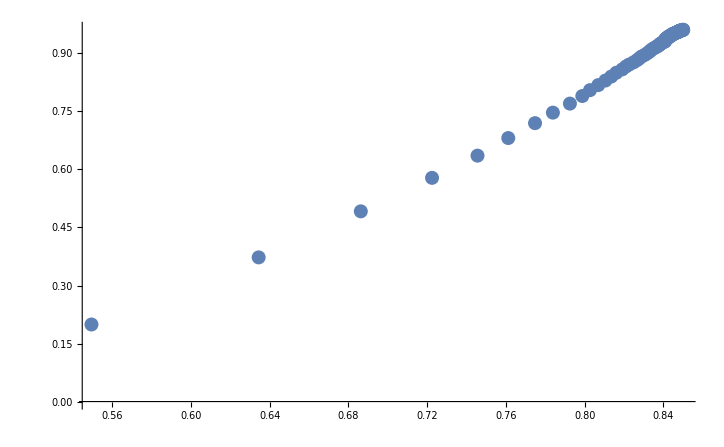

```mathematica
ListPlot[recallPrecisionFromStats/@mystats, PlotRange->All]
```